```mathematica
Today
```

Wed 2 May 2018

# Superformulaic Art

Ilkka Kokkarinen, ilkka.kokkarinen@gmail.com

Circles and rectangles are simple and familiar geometric shapes whose basic operations and mathematical formulas are straightforward enough so that schoolchildren can learn them, so we naturally use these shapes in all our non-realistic drawings and charts. However, the artistic problem with both types of basic shapes is that they are highly unnatural and will therefore always look artificial. Rectangles and polygons don’t really exist at all in nature outside human artifacts, and the few circles that do occur in nature, such as iris of the eye or the Sun, always tend to be associated with supernatural and divine, which the author suspects is not a coincidence.
The superellipse, originally grokked and popularized by the Danish mathematician Piet Hein, is the name given to the infinite family of parametric shapes that contains ordinary circles and rectangles as its trivial special cases. Instead of using the usual Euclidean distance from the center to define the circle, these distances are measured using some other norm with a real-valued exponent, the Euclidean distance being merely the special case of this norm using the exponent 2.0. The curve that forms the outer edge of the superellipse contains the points that are equidistant from the center with respect to the chosen norm.
The function selliPoint computes the coordinates of the point of the superellipse centered at cp with exponent e in the coordinate system defined by the given up and right vectors, when a is the angle (measured in radians) of the point from the center in this coordinate system. Normally the up and right vectors would be the unit vectors in vertical and horizontal axes, but being able to freely rotate and scale these two vectors allows us to rotate and scale the resulting shape.

```mathematica
selliPoint[cp_, up_, right_,e_, a_] := cp + up* Abs[Cos[a]]^(2/e)Sign[Cos[a]] + right* Abs[Sin[a]]^(2/e) Sign[Sin[a]];
selliPoints[cp_, up_, right_,e_, n_] := With[{step = 2π/n},Table[selliPoint[cp, up, right, e, a], {a,step, 2π, step}]];
```

To get an idea of how these shapes work, we can display a row of them with the exponent going from 1.5 up to 4.0 with the increments of 0.25. For rendering purposes, an arbitrary curve can be approximated from a list of points on the curve using BSplineCurve that will interpolate the intermediate points between those that are explicitly given. To ensure that there is no visible seam at the point where the curve loops back to itself at the angle 0 that is the same as angle 2π, the option SplineClosed makes this interpolation correctly look for points around that angle by looping back to the beginning. The function FilledCurve defines the area that lies inside the given closed curve that could in general be defined piecewise from different types of curve, but for our shape, the single B-Spline approximates its entire outline. Superellipse shapes are now at our full command, ready to spring into action wherever their country may need them.

```mathematica
radius[row_] := radius[row] = N[Power[1/row,1.2]];
yc[1] := 0;
yc[row_] := yc[row] = yc[row-1] + radius[row-1] + radius[row];
rowShape[row_] := With[{y = yc[row], r =radius[row]},
Table[With[{rot = RotationTransform[RandomReal[{-.05,.05}]]},FilledCurve[BSplineCurve[selliPoints[{x,y},rot[{0,.98r}],rot[{.98r,0}],RandomReal[{2,4}],40], SplineClosed-> True]]],{x,-2,12,2r}]
];

Graphics[Table[rowShape[k],{k,1,28}], ImageSize-> Large, PlotRange->{{0,10},{-1,6}}]
```

-Graphics-

All present or accounted for, sir. Now we can tell these shapes to get dressed so that we can inspect them to see how the exponent determines their general shape.

```mathematica
With[{cf = ColorData["Rainbow"]},
Graphics[{EdgeForm[{Black}],Table[{cf[RandomReal[]],
FilledCurve[BSplineCurve[selliPoints[{4(e-0.5),1},{0,.42},{.42,0},e, 60], SplineClosed -> True]]},{e,1.5,4,0.25}]}, ImageSize -> 600]]
```

-Graphics-

Using the exponent 2.0 makes the superellipse just an ordinary circle. As the exponent approaches infinity, the shape of the superellipse approaches a rectangle as the distance metric approaches the chessboard distance on the plane determined by the maximum of the horizontal and vertical distances. However, the intermediate shapes on the way towards infinity are not rounded rectangles, but more aesthetic looking shapes. Let us take a look at the exponents around 2.0, that value and the resulting perfect circle centered in the row. The shapes positioned to its right for exponents that are slightly higher than 2.0 have a more relaxed, natural and handdrawn feel to them than circles that are a little bit too perfect to be true. They could be silently used in place of circles in various technical and other documents, just to give the reader a subconscious positive impression of the document.

```mathematica
With[{cf = ColorData["SolarColors"]},
Graphics[{EdgeForm[{Thin,Black}],Table[{cf[RandomReal[]],
FilledCurve[BSplineCurve[selliPoints[{10(e-1.8),1},{0,.22},{.22,0},e, 60], SplineClosed -> True]]},{e,1.8,2.2,0.05}]}, ImageSize -> 600]]
```

-Graphics-

Superellipses with exponents lower than two become sort of lozenge shapes that bulge inwards for exponents below one, and outwards for exponent above one. Exponent of 1.0 corresponds to the Manhattan distance metric of the sum of the horizontal and vertical distances on the plane, and produces a square that is rotated by 45 degrees.

```mathematica
With[{cf = ColorData["AlpineColors"]},
Graphics[{EdgeForm[{Thin,Black}],Table[{cf[RandomReal[]],
FilledCurve[BSplineCurve[selliPoints[{2.2(e-0.2),1},{0,.2},{.2,0},e, 60], SplineClosed -> True]]},{e,0.4,1.8,0.2}]}, ImageSize -> 600]]
```

-Graphics-

Expressed as parametric regions, Wolfram Mathematica is able to do symbolic computations on superellipses. As a quick confirmation that this mechanism really works as intended, we can use it to compute the area of the unit circle, and then out of curiosity, find out the formula for the area of a superellipse where we use the exponent of 4 instead of 2.

```mathematica
selliRegion[cp_,up_,right_, e_] :=ParametricRegion[selliPoint[cp, r*up, r*right, e,a],{{r,0,1},{a,0,2π}}];
circleArea = RegionMeasure[selliRegion[{0,0},{0,1},{1,0}, 2]];
fourArea = RegionMeasure[selliRegion[{0,0},{0,1},{1,0}, 4]];
{circleArea, N[circleArea], fourArea, N[fourArea]}
```

{π,3.14159,(8 Gamma[5/4]^2)/(√π),3.70815}

Alternatively, the area could just be integrated the usual way. We can verify that for exponent of 1.0, the formula produces the rotated rectangle whose sides equal √2, the hypotenuse of a triangle whose both side lengths equal 1.

```mathematica
Integrate[1, {x,y} ∈ selliRegion[{0,0},{0,1},{1,0},1]]
```

2

With these nifty little shapes now available for us to render in an arbitrary position, we can use them to make some computational art, both static and animated. A good place to start might be to generate a random packing of superellipses of different sizes so that no two of them intersect, inspired by the page “Random space filling tiling of the plane” by on the site “Fractals, chaos, self-similarity” by Paul Bourke. The algorithm will simply create these random superellipses one at the time, rejecting those that overlap the superellipses that have already been created. The function maxRadius is given the center point cp and the list circs that contains the superellipses that have already been created, each one represented as a list structure {{x, y}, r}. As soon as one of the superellipses in this list is found to contain the center point cp inside it, the function terminates and returns -1. Otherwise the function returns the distance of the center point cp from the closest superellipse that is already in the list.

```mathematica
maxRadius[cp_, circs_,e_] := Module[{r, len, i, circ, r2,dv},
r = 1 - Norm[cp, e];
len = Length[circs];
For[i = 1, i ≤ len, i++,
circ = circs[[i]];
dv = cp-circ[[1]];
If[Abs[dv[[1]]] + Abs[dv[[2]]] < 2(r +circ[[2]]) ,
r2 = Norm[cp-circ[[1]],e];
If[r2 -circ[[2]]<0.001, Return[-1]];
r = Min[r, r2- circ[[2]]] ;
]
];
r
];
```

The next function createShapes uses the previous helper function to generate of a list of n superellipses exponent e so that none of them overlap. Each center point cp is chosen using a random radius r and angle a from the appropriate uniform distributions, but with this radius then squared and subtracted from unity to make these random points spread more uniformly over the area of the superellipse that is being filled with these random shapes. If the randomly generated center point lies sufficiently outside all existing superellipses, it is inflated to the maximum possible size to make it kiss but not cross the closest existing superellipse, but so that this superellipse also does not cross outside the superellipse area that is being filled with these superellipses.

```mathematica
τ = N[2π];
createShapes[n_,e_] := Module[{result, a,  r, d, r1,cp, n2, rc},
result = {};
n2 = n;
While[n2 > 0,
r = RandomReal[{0,1}];
r =.95(1-r^2);
a =RandomReal[{0, τ}];
cp = selliPoint[{0,0},{0,r},{r,0},e, a];
r1 = Min[maxRadius[cp, result,e],.1];
If[r1 > 0.02,
rc = Min[r1, .5(1-r)];
AppendTo[result, {cp, rc}];
n2--;
];
];
result
];
```

The list of superellipses, each one given as a pair of the form {{x, y}, r}, is then converted to graphical shapes for the display purposes. The colour of each superellipse is generated randomly, each time using one of the five randomly chosen colour gradient functions.

```mathematica
selliPacking[n_,e_] := With[{
shh = createShapes[n,e],
cfs = Map[ColorData,RandomSample[ColorData["Gradients"], 5]]
},
Graphics[{
EdgeForm[{Thin, Black}],
Table[{
RandomChoice[cfs][RandomReal[]],FilledCurve[BSplineCurve[selliPoints[s[[1]], {0,s[[2]]},{s[[2]],0},e,60], SplineClosed -> True]]
}, {s, shh}]
},
PlotRange -> {{-1,1},{-1,1}},ImageSize -> 400
]
];
```

Since the exponent of about 2.1 seems to yield the most mellow superellipses, we can try that one first.

```mathematica
selliPacking[350,2.1]
```

-Graphics-

The superellipses that are randomly generated this way will fit together nicely, regardless of the chosen exponent. A better algorithm, left as an exercise for the reader, would also move these center points around a little bit to allow some of the superellipses to inflate more and this way fill the area more tightly. The spirit of these random packings is to leave as little background showing through as possible, while maintaining the random structure of the individual shapes. This filling can always be made as tight as wanted by increasing the parameter n, but the running time of the previous simple algorithm will quickly grow intolerable as it becomes ever more difficult to find an empty spot for the next random superellipse.

```mathematica
selliPacking[400,3]
```

-Graphics-

After these static images of random algorithmic packing, the next thing for us to do is making these shapes move by creating some animated algorithmic art. Our animations will be short enough that they can be stored as animated gifs that can be immediately viewed by any web browser simply by visiting the page that contains that animated gif. To keep the following discussion and mathematics simple and straightforward, we will simply assume that the time period of the animation goes through values from 0 to 1. Once you have the function to produce the list of positions of the objects in the image at an arbitrary time t within this range, you can always generate any desired number of frames n, and this way make the animation arbitrarily long, simply by making t increase by 1 / n between two consecutive frames. 
Analogous to how the B-spline interpolation was made to loop back to beginning so as not to leave a seam to the closing point, to avoid a visible twitch at the last frame where the animation loops back to the beginning, we define the motion paths of the objects in the image in some suitably chosen way that guarantees that as each object traverses its motion path to its end position at time t = 1, this path either ends up outside the image altogether, or it ends up in the exact same position that is the position of some other object at the starting time t = 0. (This other object could even be that same object itself, in case of periodic motion.) To ensure that there is also no visible discontinuity in speed, the velocity vector of the first object at time t = 1 should equal the velocity vector of the second object at time t = 0. This whole thing is possible only if the motion is periodic over the number of frames that we render to this animation. Many interesting processes such as those computed from differential equations might not produce solutions whose periods are short enough to render using a reasonable number of frames.
Linear motion at constant speed does not generally look very natural or artistic, and is frankly suitable only if you want to make some metaphorical point about the scary mechanical uniformity of those who are different from you, which surely no dime store artist filled with resentment towards society has not done before. One simple trick to smooth linear motion is to squeeze and stretch the passage of time instead, which then indirectly causes the motion that is computed linearly with respect to that time to also squeeze and stretch accordingly. In fact, since there is no mathematical difference between positions of time, space or colour, each one of these really just being a dimensionless number on which we impose an interpretation to mean something in the image, there is also no law of nature or man that dictates that it must always be the same time everywhere in the same image frame, any more than there would be a law that says that some pixel must have the same colour at all times! The handy function ease makes the linear motion to first accelerate and then decelerate at rate defined by the adjustable exponent parameter e.

```mathematica
ease[t_,e_] :=With[{tt =t-Floor[t]},
Floor[t] + Piecewise[{
{.5Power[2tt,e], tt<.5},
{1-.5Power[2(1-tt),e], tt <= 1}
}]];
```

Plotting this motion with respect to time for a couple of different exponents shows what is going on. The exponent of 1 produces linear motion, whereas higher exponents lengthen the initial acceleration and final deceleration. An exponent less than one works the opposite so that it makes the motion to be fast in the beginning and end, and slow down in the middle. All four curves will still reach the exact same target point at time t = 1.

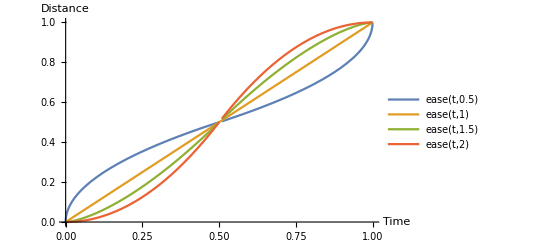

```mathematica
Plot[{ease[t,.5], ease[t,1],ease[t,1.5], ease[t,2]}, {t, 0, 1}, PlotLegends -> "Expressions", AxesLabel -> {"Time", "Distance"}]
```

The example animation that we will go through step by step renders multiple columns of superellipses where the superellipses move upwards in a crawling fashion, as if they were pushing themselves forward by repated muscle action. To tell these objects apart within the mathematical formulation, each object is indexed with two variables row and col, and the function position computes the position of that object at time t. To ensure that the continuity requirement position[row, col, 1] == position[row, col + 1, 0] holds throughout the entire grid of objects, we compute the position of each object as a function of row and col + t to make this equation trivially true regardless of which continuous function is actually used to compute the position. (To the latter term, anything whose differential with respect to col + t can be added without affecting the result.) The familiar sine and cosine functions will often come handy in creating periodic motion that finished up at t = 1 in the exact same position that it originally started at t = 0. Since the period of both of these functions is 2π, the current time must be multiplied by 2kπ in these calculations, where k is the frequency of the motion measured in Hertz. Adding up sine waves with different frequencies could in principle generate any motion curve whatsoever.

```mathematica
position[row_, col_, t_] := 
With[{ct = col + t + .07row},
{row + .02Cos[.3ct] + .01Sin[.2 (ct + .25row)], ease[ct,1.2] }
];
```

Since the position formula is a symbolic mathematical expression, we can verify the position continuity requirement easily. In fact, it is just as easy to verify that not merely the object positions, but also their velocities, accelerations, jerks and jounces are smooth and continuous.

```mathematica
Table[(Nest[D,position[row,col,t],k] /. t -> 1)== (Nest[D,position[row,col + 1,t],k] /. t -> 0),{k, 0, 4}]
```

{True,True,True,True,True}

Having defined the position of each object at the given time, the next thing to decide is what each object looks like. We render each object as a superellipse of the nice exponent 2.2. To make this animation more interesting, instead of having these shapes traipse around the flat and boring two-dimensional Cartesian plane, we allow the caller to provide an arbitrary transformation function that maps the points (x, y) to some other points. Note that this transformation has to be applied to each point on the edge of the shape, not just the center point of the shape.

```mathematica
shape[row_, col_, t_, trans_] := With[{cp = position[row, col, t]},
FilledCurve[BSplineCurve[Map[trans,selliPoints[cp, {0,.15},{.2,0},2.2,60]], SplineClosed -> True]]
];
```

With the ability to generate the graphical shape of every object for the arbitrary point in time, it is easy to write the function to produce the image that displays all the shapes at once. The powerful function Graphics generates a graphical display of the (possibly nested list) of shapes given to it, with a myriad of options to set the colour, line thickness and other rendering parameters. The shapes and the options are rendered in the order that they are listed in, which will affect the result in situations where the shapes partially overlap each other. The graphical display forms a two-dimensional peephole to the infinite plane that all these shapes reside, so we have to remember set the boundaries with the option PlotRange in a way that displays only the space that we want to end up showing to the viewer. Leaving the objects on the edge of the image partially visible conveys the information that there more objects marching outside the image, whereas leaving margins around the image tells the viewer that these are the only objects that exist inside the made-up microworld that the rendering makes visible to the viewer.
Since we use a simple perspective projection to transform the points on the plane with the viewer eye hovering over the origin, the simplest way to do these calculations is to define the origin point (0, 0) to be at the center of the peephole, and all other points (x, y) are projected to the viewer by dividing their coordinates on the height value z defined for that point. Since the shape rows and columns are incremented with step size 0.5, each shape moves over one shape in between when time goes from 0 to 1, and we can make shapes alternate between black and white colour and still keep the transition seamless.

```mathematica
curvyfield[{x_,y_}] := With[{z = .5Cos[x+y] + .2Sin[2x-.5y]},
{x/(z+5), y/(z+5)}
];
selliCrawl[t_, trans_] :=Image[Graphics[{
EdgeForm[{Thick, Black}],Table[{If[Mod[2*row+2*col,2]==0,White,GrayLevel[.2+.03Cos[.2col +.1row]]],shape[row, col,t, trans]}, {row, -7,7,.5},{col, -7, 7,.5}]
}, ImageSize -> 500, PlotRange -> {{-.8,.8},{-.8,.8}}]];
selliCrawl[.2, curvyfield]
```

-Graphics-

Using a different function to define the height field would produce a rather different result.

```mathematica
jaggyfield[{x_,y_}] := With[{ z = .2TriangleWave[ChessboardDistance[{x,y},{0,0}]]},
{x/(z+5), y/(z+5)}
];
selliCrawl[.5,jaggyfield]
```

-Graphics-

And it is not like the transformation is even required to maintain overall shape of the space as a Cartesian plane.

```mathematica
spiral[{x_,y_}] :=With[{sa = (x+7) *π/7, r = .2y},selliPoint[{0,0},{0,r},{r,0},2,sa+y*π/20]];
selliCrawl[0, spiral]
```

-Graphics-

Armed with the ability to produce the image frame for the given time t, exporting the result as an animated gif is a one-liner with the help of Mathematica’s Swiss army knife Export that, just like Import to the opposite direction, can export the data in every standard data format known to man. But before exporting the frames into that animated gif, we should experiment with some image processing operations to make these images look more natural and artistic. Especially the image deconvolution operation has the effect of eliminating the pixellation from the image, with an infinite variety of kernels available to produce all kinds of more or less glitchy effects. The function Blend can be used to compose images with the given proportional weight for each image. These weights can even be negative numbers to subtract that image from the total composition.

```mathematica
frame[t_] := With[{im = selliCrawl[t, curvyfield]},
Blend[{
ImageDeconvolve[im,{{-.1,.2,.2},{-.2,1,-.2},{-.1,.2,-.3}}],
ImageConvolve[im,{{0,-.1,.1,.3,.3},{-.3,0,0,.1,0},{0,-.1,.3,0,0},{0,.1,.3,0,-.3},{-.1,0,0,0,.3}}]
},{2,1}]];
frame[.3]
```

-Graphics-

To export these frames together as one animated gif, basically the only thing for us left to decide is the length of a single animation frame, and the function Export will do all the rest. Since the frames for the points in time t = 0 and t = 1 are identical, you should remember to leave either one of them out of the table of images that you give to Export, as otherwise your animation will have a noticeable twitch delay at that point. Some glitch art can occasionally be an improvement over smooth mathematical continuity, but in this particular situations that will rarely be the case.

```mathematica
Export["/Users/ilkkakokkarinen/Desktop/Ilkka/WolframExamples/superellipsecrawl.gif", Table[frame[t],{t,1/13,1,1/13}], "DisplayDurations" -> 0.05]
```

/Users/ilkkakokkarinen/Desktop/Ilkka/WolframExamples/superellipsecrawl.gif

The resulting 500-by-500 image of 13 frames takes about 1.6 megabytes to store as an animated gif, still small enough for all the tumblerinas to post under the present image size limitations. Remember that the number of pixels in the image grows as a square, so the difference in image size from a small change can be quite dramatic. Images whose shapes are axis-aligned also compress much better than those with shapes at arbitrary orientations.
As with many other parametric curves f(t), using the superellipse edge itself as an animation path has the problem that the path f(t) does not advance with a constant speed with respect to its parameter t. If you divide the interval from 0 to 2π into equal intervals and plot these points of the superellipse, these points are heavily concentrated in the corners, the more so the higher the exponent of the superellipse. To place these points symmetrically on equal lengths, some more mathematics is needed to compute the parameter values for these points. Since the symbolic equations can get a bit hairy, we will do a numerical approximation good enough for the artistic rendering. Suppose we the points of the superellipse around a Archimedean spiral where the radius grows linearly with respect to the angle, with the functon spiralPoint giving us these coordinates converted to superellipse whose exponent equals five. The function succAngle uses binary search to find the angle a from the interval [as, ae] so that the distance between spiralPoint[a] and spiralPoint[as] is close enough to d.

```mathematica
tau = N[2π];
radius[angle_] := Power[angle,.89];
spiralPoint[angle_] := With[{r = radius[angle]},
selliPoint[{0,0},{0,r},{r,0},5,angle]];
succAngle[as_,ae_, d_] := Module[{cs, ce, cm, sp},
cs = as;
ce = ae;
sp = spiralPoint[as];
While[ce - cs > tau/3000,
cm = cs + (ce - cs) / 2;
If[EuclideanDistance[spiralPoint[cm], sp] > d,ce = cm, cs = cm]
];
cm
];
```

Generating the angles that produce the spiral can now be done with NestWhileList until the target goal angle has been reached. Each point is rendered as a slice between the angles as and ae with using the radiuses for this round and the next round (which we get simply by adding 2π to the angle) to limit the slice. The slices are rendered using random colours, but to make the colour around the spiral a bit smoother, the colour function  for each integer interval of the angles is chosen randomly and memoized to keep it consistent with the other slices inside that same interval. The colour of the slice is then interpolated from its colour inside the current interval and the final colour of the previous interval, with the weight of the previous colour falling with respect to the square of the distance.

```mathematica
ClearAll[colour];
colour[idx_]:= colour[idx] = ColorData[RandomChoice[ColorData["Gradients"]]];
sliceColour[a_] := With[{aa = .3a},With[{i = Floor[aa], v = Mod[aa,1]},Blend[{
colour[i][v], colour[i-1][1]
},{1-v^2,v^2}]]];
slice[{as_,ae_}] :={
sliceColour[ae],
EdgeForm[{Black, Thickness[.00004as]}],
FilledCurve[BSplineCurve[
Join[{spiralPoint[ae],spiralPoint[as]},
Table[spiralPoint[tau+aa],{aa, as,ae,(ae-as)/5}]
]
, SplineClosed->True]]
};
 spiralImage [angles_]:= ImageDeconvolve[Graphics[{
Table[slice[p], {p, Partition[angles,2,1]}]
}, Background -> GrayLevel[.95],ImageSize -> Large, PlotRange -> {{-39,41},{-39,41}}],{{.3,.5,0,-.5},{0,.5,.5,-.3},{.5,0,-.5,.3},{-.3,.5,-.5,0}}];
spiralImage[NestWhileList[(succAngle[ #, #+tau/4, .15#])&,tau/4, (# < 9tau)&]]
```

-Graphics-

For comparison purposes, here is the same construction without first correcting the angles, which results in rather inelegant distortion in the slice widths based on their angles.

```mathematica
spiralImage[Table[a,{a,tau,9tau,tau/40}]]
```

-Graphics-

Since nothing in the symbolic formula that computed the points of the superellipse requires that these vectors and points are two-dimensional, the exact same symbolic formulas can compute and render superellipses in three-dimensional space as solid Tube volumes instead of two-dimensional curves and areas. A nested structure of superellipses, again inspired by the fractal site of Paul Bourke, is easy to define using recursion in which the points on the edge of the superellipse become the center points of the smaller superellipses wrapped around it. As is convenient in this sort of definitions, the recursive function receives as arguments an arbitrary center point cp and three vectors up, right and front that determine its orientation in three-dimensional space. Normally these three vectors are orthonormal, but there is no law of nature or man demanding that they would have to be that way. The orientation of a smaller ring wrapped around the parent superellipse tube defined at the previous level of recursion can be computed from the orientation vectors of the parent superellipse.

```mathematica
cf = ColorData["AlpineColors"];
bf = 12;
ep[cp_,up_,right_,front_,i_] := selliPoint[cp,up,right,3,i*N[2π/bf]];
ring[cp_,up_,right_,front_,0] := {cf[RandomReal[]],Specularity[White,15],Tube[BSplineCurve[selliPoints[cp,up,right,3,40], SplineClosed -> True],.2Norm[up]]};
ring[cp_,up_,right_,front_,d_/; d > 0] := {
ring[cp,up,right,front,0],
Table[With[{p1 = ep[cp,up,right,front,i],p2 = ep[cp,up,right,front, i+1]},
ring[p1, front/2.5,(p1-cp)/2.5,(p2-p1)/2,d-1]],{i,0,bf - 1}]
};

With[{im = Image[Graphics3D[ring[{0,0,0},{0,1,0},{1,0,0},{0,0,1},2], ViewPoint->{1,-1,2},ViewAngle -> 26 Degree,Boxed -> False, Lighting -> {{"Point",Orange,{-1,-1,2}},{"Point",White,{1,3,3}}}], ImageSize -> 600]},
MeanShiftFilter[Blend[{
PeronaMalikFilter[im,2],
RidgeFilter[im, 2],
ImageDeconvolve[im, {{-.5,.2,-.2,0,0},{0,.2,.5,.5,0},{.5,.5,0,0,.2},{-.5,0,-.2,0,-.2}}]
},{3,-1,3}
],2,1]]
```

-Graphics-

Two spot lights and specularly reflective surfaces give a bit of shine to the rendered shape, followed by some image effects, just to try them out. However, trying to render this series of tubes using the Mathematica installation on author’s computer tends to make it somehow run past some internal limit and crash. Let us change the definition for the base case slightly to use a simpler shape of cylinders will ball joints, similar to models used to illustrate molecules in chemistry, to see if this might help us render this fractal deeper. We can also try out a different lighting so that there is a gray ambient light everywhere regardless of the position, and green and yellow spot lights placed inside and outside the structure providing the rest of the illumination, for sort of an arboreal result.

```mathematica
cf = ColorData["Rainbow"];
bf = 8;
ep[cp_,up_,right_,front_,i_] := selliPoint[cp,up,right,2,i*N[2π/bf]];
ring[cp_,up_,right_,front_,0] := {cf[RandomReal[]],Specularity[GrayLevel[.4],10],Table[With[{p1 = ep[cp,up,right,front,i],p2 = ep[cp,up,right,front, i+1]},
{Cylinder[{p1,p2},Norm[up]/14], Sphere[p1,Norm[up]/6]}],{i,0,bf-1}]};
With[{im = Image[Graphics3D[{EdgeForm[],ring[{0,0,0},{0,1,0},{1,0,0},{0,0,1},4]}, ViewPoint->{1,-2,3},ViewAngle -> 14 Degree,Boxed -> False, Lighting -> {{"Ambient", GrayLevel[.3]},{"Spot",Green,{1,-1,1.7},20 Degree},{"Spot",Yellow,{-1,-3,3}, 90 Degree}}
], ImageSize -> 600]},
Blend[{
HarmonicMeanFilter[im,1],
GaussianFilter[im,1],
KuwaharaFilter[im,2]
}]]
```

-Graphics-